```mathematica
(* Nahrame si obrazok *)
img=-Graphics-;
```

```mathematica
(* aplikacia odfarbovania zachovavajuceho kontrast *)
imgGrayscale=ImageEffect[img,"Decolorization"]
```

-Graphics-

```mathematica
(* Prevedieme obrazok na pole hodnot pixelov *)
ImageData[imgGrayscale][[{1,2}]];
ImageData[img][[{1,2}]];
(* Prevedieme pole hodnot pixelov na obrazok *)
ArrayPlot[ImageData[imgGrayscale],ColorFunction->GrayLevel]
```

-Graphics-

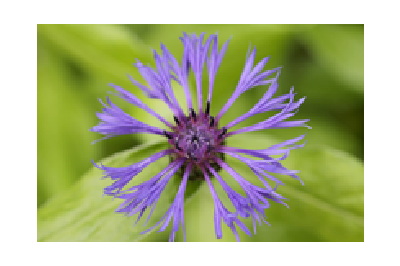
```mathematica
(* Rozklad do troch RGB kanalov *)
cimg=-Graphics-;
GraphicsRow[Prepend[MapThread[ArrayPlot[ImageData[#1],ColorFunction->#2]&,{ColorSeparate[cimg],{RGBColor[#,0,0]&,RGBColor[0,#,0]&,RGBColor[0,0,#]&}}],cimg]]
```

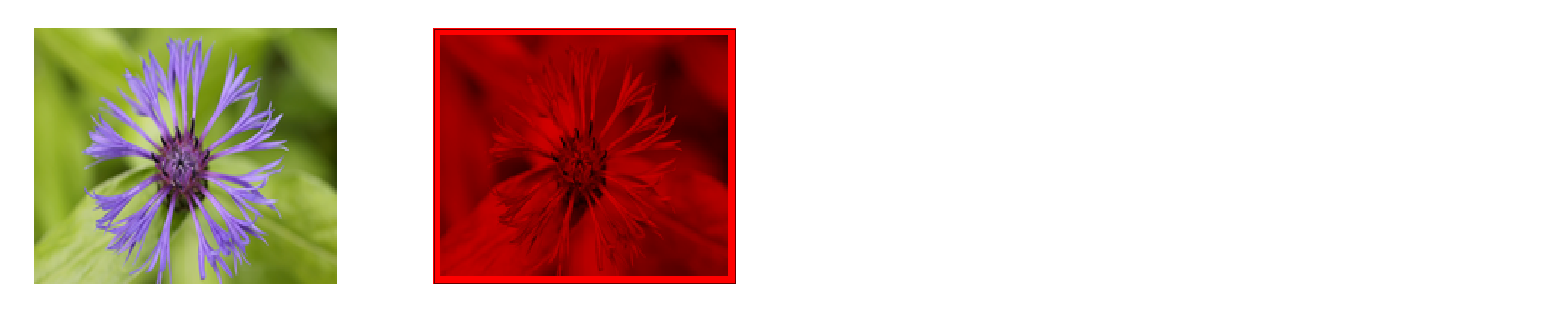

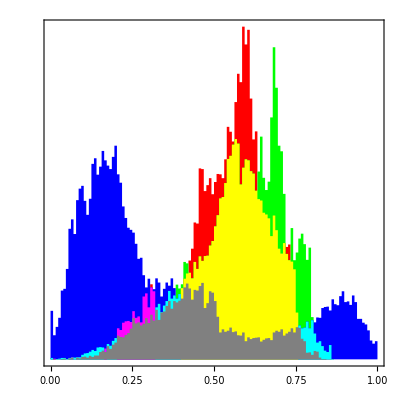

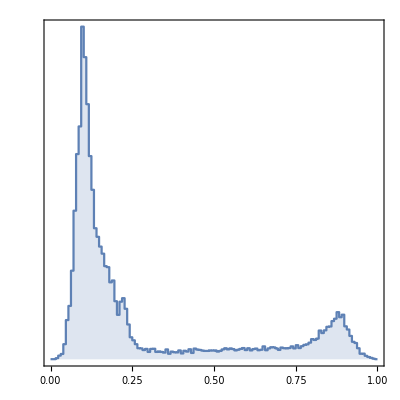

```mathematica
(* graficka reprezentacia obrazku pomocou histogramu *)
GraphicsRow[{img,ImageHistogram[img,FrameTicks->{Automatic,None},AspectRatio->1]}]
GraphicsRow[{imgGrayscale,ImageHistogram[imgGrayscale,FrameTicks->{Automatic,None},AspectRatio->1]}]
```